```mathematica
plotOffGasFileCO2[svnPath_,strainPath_]:= 
With[{matrixCO2=Import[svnPath<>"/Chemostat analysis/chemostatAnalysis/data/"<>strainPath<>"/offGas.csv"]},DateListPlot[
Transpose[{matrixCO2[[2;;All,1]],matrixCO2[[2;;All,2]]}],PlotLegends->"CO_2%"]
]
plotOffGasFileEtOH[svnPath_,strainPath_]:= 
With[{matrixEtOH=Import[svnPath<>"/Chemostat analysis/chemostatAnalysis/data/"<>strainPath<>"/offGas.csv"]},DateListPlot[
Transpose[{matrixEtOH[[2;;All,1]],matrixEtOH[[2;;All,4]]}],PlotLegends->"EtOH [ppm]"]
]
plotOffGasFileO2[svnPath_,strainPath_]:= 
With[{matrixO2=Import[svnPath<>"/Chemostat analysis/chemostatAnalysis/data/"<>strainPath<>"/offGas.csv"]},DateListPlot[
Transpose[{matrixO2[[2;;All,1]],matrixO2[[2;;All,5]]}],PlotLegends->"O_2%"]
]
plotOffGasAll[svnPath_,strainPath_] :=
With[{matrix=Import[svnPath<>"/Chemostat analysis/chemostatAnalysis/data/"<>strainPath<>"/offGas.csv"]},
{DateListPlot[
Transpose[{matrix[[2;;All,1]],matrix[[2;;All,2]]}],PlotLegends->"CO_2%"],DateListPlot[
Transpose[{matrix[[2;;All,1]],matrix[[2;;All,4]]}],PlotLegends->"EtOH [ppm]"],DateListPlot[
Transpose[{matrix[[2;;All,1]],matrix[[2;;All,5]]}],PlotLegends->"O_2%"
]
}
]
svnPath ="~/Dropbox/School/mblab"
```

YMR037C/06.24.14/chem4

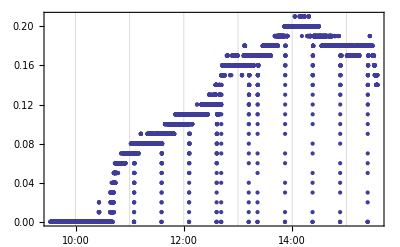

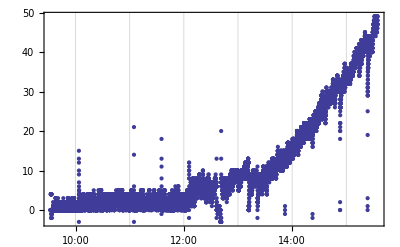

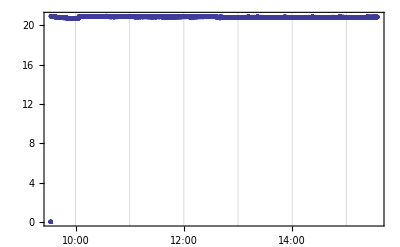

YMR037C/05.29.14/chem4

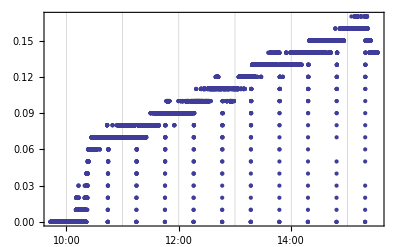

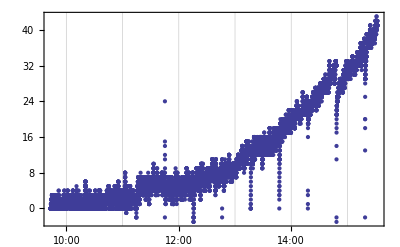

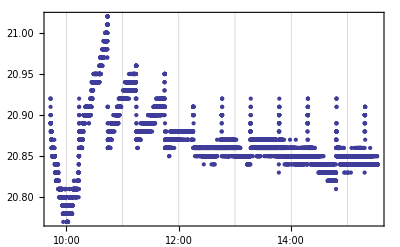

```mathematica
strainPath = "YMR037C/06.24.14/chem4"
plotOffGasFileCO2[svnPath,strainPath]
plotOffGasFileEtOH[svnPath,strainPath]
plotOffGasFileO2[svnPath,strainPath]
strainPath = "YMR037C/05.29.14/chem4"
plotOffGasFileCO2[svnPath,strainPath]
plotOffGasFileEtOH[svnPath,strainPath]
plotOffGasFileO2[svnPath,strainPath]
```

YKL062W/06.09.14/chem8

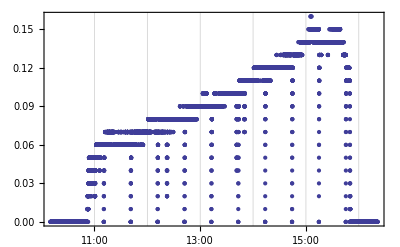

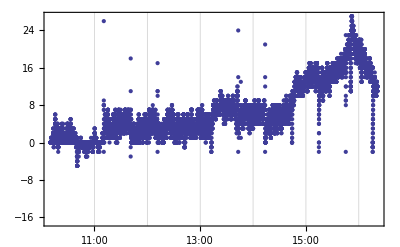

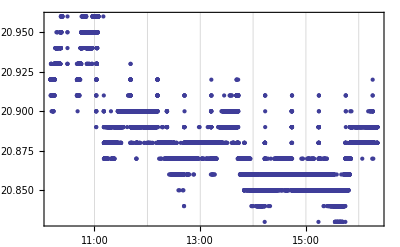

YKL062W/06.13.14/chem4

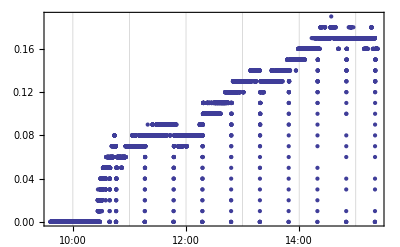

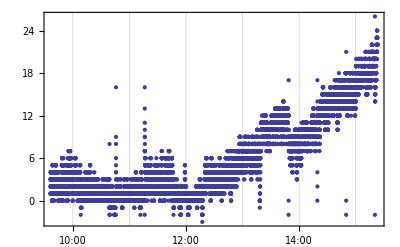

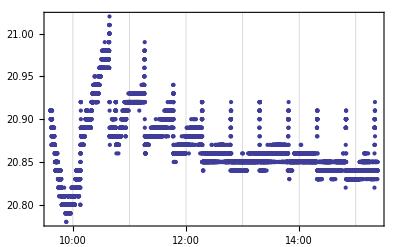

```mathematica
strainPath = "YKL062W/06.09.14/chem8"
plotOffGasFileCO2[svnPath,strainPath]
plotOffGasFileEtOH[svnPath,strainPath]
plotOffGasFileO2[svnPath,strainPath]
strainPath = "YKL062W/06.13.14/chem4"
plotOffGasFileCO2[svnPath,strainPath]
plotOffGasFileEtOH[svnPath,strainPath]
plotOffGasFileO2[svnPath,strainPath]
```

YNL199C/06.23.14/chem8

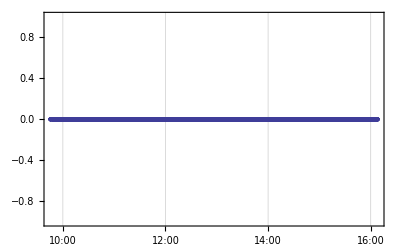

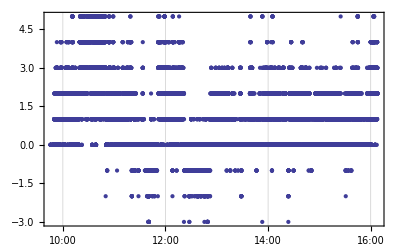

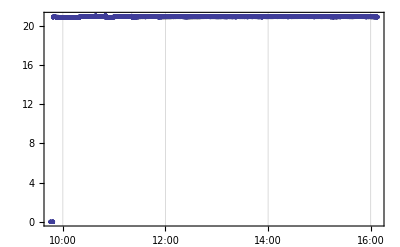

```mathematica
strainPath = "YNL199C/06.23.14/chem8"
plotOffGasFileCO2[svnPath,strainPath]
plotOffGasFileEtOH[svnPath,strainPath]
plotOffGasFileO2[svnPath,strainPath]
```